```mathematica
<<TernarySearch`
```

```mathematica
Xpts=20;
Ypts=30;
```

## TernarySearch

### Define function

```mathematica
F[x_]:=x^2;
```

### Search the minimum

```mathematica
ts=TernarySearch[F,-10,40,10^(-5)];
leftSearch=ts[["leftSearch"]];
rightSearch=ts[["rightSearch"]];
minposval=ts[["leftSearch"]][[-1]]//N
```

{-8.16183×10^-7,6.66155×10^-13}

### Plot intermediate guesses

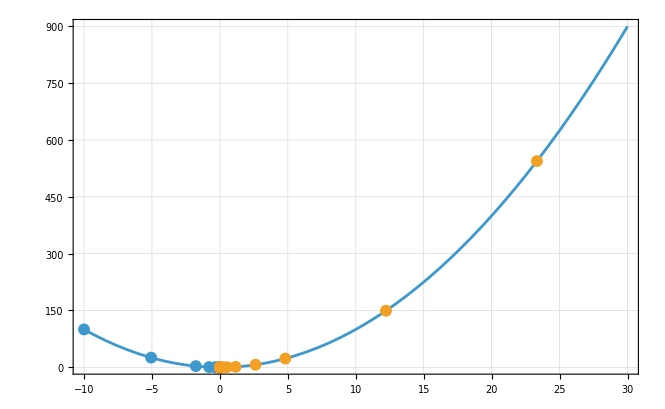

```mathematica
Show[
Plot[F[x],{x,-10,30},Frame->True,GridLines->Automatic],
ListPlot[{leftSearch,rightSearch}]
]
```